```mathematica
1、指数函数的展开
```

```mathematica
Maclaurin级数
```

```mathematica
Normal[Series[Exp[x],{x,0,9}]]
```

```mathematica
逼近的效果（在x=0处展开）
```

```mathematica
Manipulate[Plot[{Exp[x],Evaluate[Normal[Series[Exp[x],{x,0,n}]]]},{x,-20,5},
PlotRange->{-5,20},PlotStyle->{{Red,Thick},{Blue}},
Filling->{1->{2}},FillingStyle->LightYellow,
AspectRatio->Automatic],{n,1,30,1}]
```

```mathematica
Manipulate[Plot[{Exp[x],Evaluate[Table[Normal[Series[Exp[x],{x,0,m}]],{m,n}]]},{x,-10,5},
Filling->{1->{n}},
PlotRange->{-5,10},AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
Taylor级数（在x=1处展开）
```

```mathematica
Normal[Series[Exp[x],{x,1,9}]]
```

```mathematica
Manipulate[Plot[{Exp[x],Evaluate[Normal[Series[Exp[x],{x,1,n}]]]},{x,-20,5},
PlotRange->{-5,20},PlotStyle->{{Red,Thick},{Blue}},
Filling->{1->{2}},FillingStyle->LightYellow,
AspectRatio->Automatic],{n,1,30,1}]
```

```mathematica
2、正弦函数的展开
```

```mathematica
Normal[Series[Exp[x],{x,0,9}]]
```

```mathematica
Maclaurin级数（在x=0处展开）
```

```mathematica
Manipulate[Plot[{Sin[x],Evaluate[Table[Normal[Series[Sin[x],{x,0,m}]],{m,2n-1}]]},{x,-3Pi,3Pi},
Filling->{1->{2n-1}},
PlotRange->3,AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
Taylor级数（在x=π处展开）
```

```mathematica
Normal[Series[Exp[x],{x,Pi,9}]]
```

```mathematica
Manipulate[Plot[{Sin[x],Evaluate[Table[Normal[Series[Sin[x],{x,Pi,m}]],{m,2n-1}]]},{x,-3Pi,3Pi},
Filling->{1->{2n-1}},
PlotRange->3,AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
3、反正切函数的展开
```

```mathematica
Normal[Series[ArcTan[x],{x,0,9}]]
```

```mathematica
在原点(x=0)处的展开
```

```mathematica
Manipulate[Plot[{ArcTan[x],Evaluate[Normal[Series[ArcTan[x],{x,0,n}]]]},{x,-5,5},
PlotRange->{-5,5},PlotStyle->{{Red,Thick},{Blue}},
Filling->{1->{2}},FillingStyle->LightYellow,
AspectRatio->Automatic],{n,1,30,1}]
```

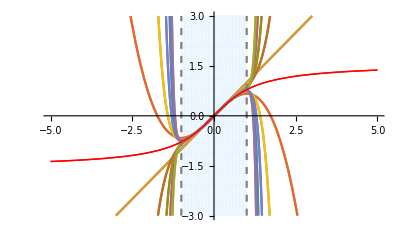

```mathematica
f1=Plot[ArcTan[x],{x,-5,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[Normal[Series[ArcTan[x],{x,0,n}]],{n,20}]],{x,-3,3},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f3=RegionPlot[-1<x<1,{x,-1,1},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f3,f2,f4,f1]
```

```mathematica
在无穷远点(1/x=0)处展开
```

```mathematica
Normal[Series[ArcTan[x],{x,Infinity,9}]]
```

```mathematica
f1=Plot[ArcTan[x],{x,-5,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[-Pi/2-Sum[(-1)^(n)/((2n+1)x^(2n+1)),{n,0,m}],{m,0,15}]],{x,-5,-0.2},PlotRange->3];
f3=Plot[Evaluate[Table[Pi/2-Sum[(-1)^(n)/((2n+1)x^(2n+1)),{n,0,m}],{m,0,15}]],{x,0.2,5},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f5=RegionPlot[x<-1||x>1,{x,-5,5},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f5,f2,f3,f4,f1]
```

```mathematica
4、1/(1+x)的展开
```

```mathematica
Normal[Series[1/(1+x),{x,0,9}]]
```

```mathematica
在原点(x=0)处的展开
```

```mathematica
Manipulate[Plot[{1/(1+x),Evaluate[Normal[Series[1/(1+x),{x,0,n}]]]},{x,-1,5},
PlotRange->{-2,4},PlotStyle->{{Red,Thick},{Blue}},
Filling->{1->{2}},FillingStyle->LightYellow,
AspectRatio->Automatic],{n,1,30,1}]
```

```mathematica
f1=Plot[1/(1+x),{x,-1,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[Normal[Series[1/(1+x),{x,0,n}]],{n,20}]],{x,-3,3},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f3=RegionPlot[-1<x<1,{x,-1,1},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f3,f2,f4,f1]
```

```mathematica
在无穷远点(1/x=0)处展开
```

```mathematica
Normal[Series[1/(1+x),{x,Infinity,9}]]
```

```mathematica
Manipulate[Plot[{1/(1+x),Evaluate[Normal[Series[1/(1+x),{x,Infinity,n}]]]},{x,-1,5},
PlotRange->{-2,4},PlotStyle->{{Red,Thick},{Blue}},
Filling->{1->{2}},FillingStyle->LightYellow,
AspectRatio->Automatic],{n,1,30,1}]
```

```mathematica
f1=Plot[1/(1+x),{x,-1,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[Normal[Series[1/(1+x),{x,Infinity,n}]],{n,20}]],{x,-1,5},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f5=RegionPlot[x<-1||x>1,{x,-1,5},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f5,f2,f4,f1]
```